```mathematica
i={0,0.25,0.5,0.75,1,1.25,1.5,1.75,2,2.25,2.5,2.75,3,3.25,3.5,3.75,4,4.25,4.5};
Bup={6,94,180,265,351,442,526,612,713,784,873,950,1034,1105,1157,1207,1250,1285,1319};
Bdown={7,98,188,276,362,450,536,624,712,796,883,962,1041,1113,1168,1214,1255,1288,1319};
```

FittedModel[11.9166+310.148 x+37.3301 x^2-9.30819 x^3]

FittedModel[15.3035+316.644 x+35.7725 x^2-9.30319 x^3]

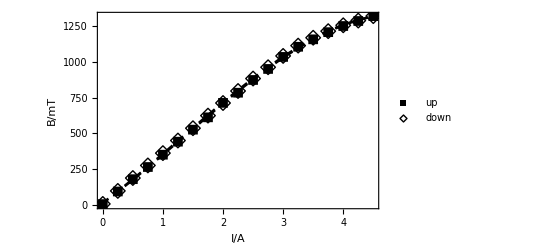

```mathematica
dataup=Transpose[{i,Bup}];
nlmup=NonlinearModelFit[dataup,a x^3+b x^2+c x +d,{a,b,c,d},x]
Normal[nlmup];
datadown=Transpose[{i,Bdown}];
nlmdown=NonlinearModelFit[datadown,a x^3+b x^2+c x +d,{a,b,c,d},x]
Normal[nlmdown];
Show[ListPlot[dataup,PlotStyle->{PointSize[0.02],Black},PlotMarkers->{"■",10},PlotLegends->{"up"}],Plot[nlmup[x],{x,0,4.6},PlotStyle->{Dashed, Black}],ListPlot[datadown,PlotStyle->{PointSize[0.02],Black},PlotMarkers->{"◇",15},PlotLegends->{"down"}],Plot[nlmdown[x],{x,0,4.6},PlotStyle->{Dashed, Black}],Frame->True,FrameLabel->{Ι/A,B/mT}]
```

```mathematica
nlmup["BestFit"]
```

11.9166+310.148 x+37.3301 x^2-9.30819 x^3

```mathematica
nlmup["ParameterErrors"]
```

{0.659448,4.51983,8.61264,4.35409}

```mathematica
nlmup["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -9.30819 | 0.659448 | -14.1151 | 4.56559×10^-10
b | 37.3301 | 4.51983 | 8.25917 | 5.80189×10^-7
c | 310.148 | 8.61264 | 36.0108 | 5.56663×10^-16
d | 11.9166 | 4.35409 | 2.73688 | 0.0152843

```mathematica
nlmav[x_]:=1/2*(nlmup[x]+nlmdown[x])
```

```mathematica
nlmav[1.5]
nlmav[2]
nlmav[4.21]

nlmav[1.18]
nlmav[2.01]
nlmav[4.68]
```

534.538

712.162

1286.47

419.022

715.639

1327.

```mathematica
B[DK_,DK0_,DK1_,DK2_]:=1/0.467*1/(2*0.2)*(DK2^2-DK1^2)/(DK0^2-DK^2)
(*Abs[(DK0^2-DK1^2)]+Abs[(DK0^2-DK2^2)]*)
```

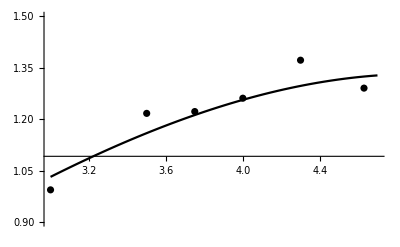

```mathematica
Bcalc={B[431.51,
595.03,
582.16,
608.33
],
B[430.04,
590.11,
575.79,
607.17
],
B[428.68,
593.23,
578.18,
610.48
],
B[429.11,
592.20,
575.15,
608.31
],
B[429.22,
588.75,
574.06,
609.24
],
B[429.82,
594.65,
578.84,
613.00
]};
icalc={3,3.5,3.75,4,4.3,4.63};
dataBcalc=Transpose[{icalc,Bcalc}];
Show[ListPlot[dataBcalc,PlotStyle->Black],Plot[nlmav[x]/1000,{x,3,4.7},PlotStyle->Black],PlotRange->{{3,4.7},{0.9,1.5}}]
```

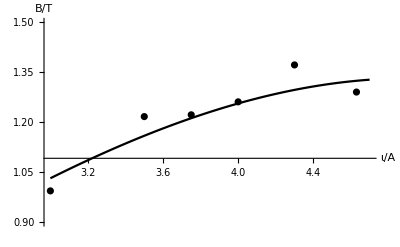

```mathematica
Show[%152,AxesLabel->{HoldForm[ι/A],HoldForm[B/T]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Btheory={0,0,0,0,0,0};
For[i=1,i≤6,i++,
Btheory[[i]]=nlmav[icalc[[i]]]]
Bcalc
Btheory/1000
```

{0.993587,1.21695,1.22229,1.26126,1.37226,1.29069}

{1.03151,1.15927,1.21212,1.25645,1.29718,1.32456}

```mathematica
Transpose[{Bcalc,Btheory/1000}]
```

{{0.993587,1.03151},{1.21695,1.15927},{1.22229,1.21212},{1.26126,1.25645},{1.37226,1.29718},{1.29069,1.32456}}

```mathematica
TableForm[Transpose[%163]]
```

0.993587 | 1.21695 | 1.22229 | 1.26126 | 1.37226 | 1.29069
1.03151 | 1.15927 | 1.21212 | 1.25645 | 1.29718 | 1.32456

```mathematica
Grid[%165]
```

0.993587 | 1.21695 | 1.22229 | 1.26126 | 1.37226 | 1.29069
1.03151 | 1.15927 | 1.21212 | 1.25645 | 1.29718 | 1.32456

```mathematica
DB[DK_,DK0_,DK1_,DK2_,dDK_,dDK0_,dDK1_,dDK2_]:=Module[{aa,cc,x,y,z,w},aa={x->DK,y->DK0,z->DK1,w->DK2};SqrtSum[a_,b_,c_,d_]:=Sqrt[a^2+b^2+c^2+d^2];cc=SqrtSum[dDK*D[B[x,y,z,w],x]/.aa,dDK0*D[B[x,y,z,w],y]/.aa,dDK1*D[B[x,y,z,w],z]/.aa,dDK2*D[B[x,y,z,w],w]/.aa];
cc];
B[429.22,
588.75,
574.06,
609.24]
DB[429.22,
588.75,
574.06,
609.24,1,1,1,1]
```

1.37226

0.0565453

```mathematica
0.0565453/1.37226
```

0.041206

```mathematica
a=4.*10^6;
R1[K_]:=Sqrt[1-K*546.1/a]
R2[K_]:=Sqrt[1-K*576.959/a]
R3[K_]:=Sqrt[1-K*579.065/a]
a/546.1
a/576.959
a/579

Graphics[Flatten[{Table[{Red,Circle[{0,0},R1[k]]},{k,7320,7324}],Table[{Blue,Circle[{0,0},R2[k]]},{k,6928,6932}],Table[{Blue,Circle[{0,0},R3[k]]},{k,6903,6907}]}]],
Graphics[Table[{Blue,Circle[{0,0},R3[k]]},{k,6903,6907}]]

Graphics[Table[{Red,Circle[{0,0},R1[k]]},{k,7320,7324}]]
Graphics[Flatten[{Table[{Blue,Circle[{0,0},R2[k]]},{k,6925,6932}],Table[{Blue,Circle[{0,0},R3[k]]},{k,6900,6907}]}]]
```

7324.67

6932.9

6908.46

Syntax::tsntxi: "Graphics[Flatten[{Table[{Red,Circle[{0,0},R1[k]]},{k,7320,7324}],Table[{Blue,«1»},«1»],Table[{Blue,Circle[{0,0},R3[k]]},{k,6903,6907}]}]],«1»" 不完整；需要更多输入.

7326.99

6934.77

6909.55

546.221

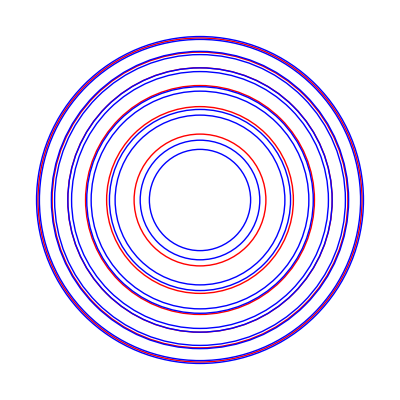

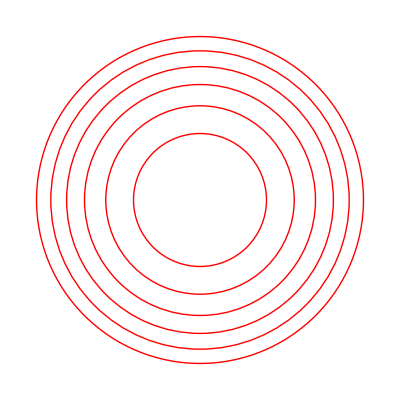

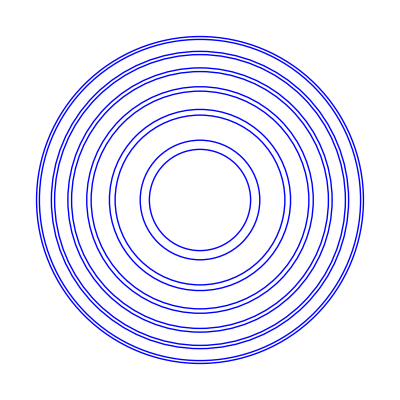

```mathematica
a=4.*10^6;
R1[K_]:=Sqrt[(a/(K*546.074/1.00027))^2-1]
R2[K_]:=Sqrt[(a/(K*576.959/1.00027))^2-1]
R3[K_]:=Sqrt[(a/(K*579.065/1.00027))^2-1]
a/(546.074/1.00027)
a/(576.959/1.00027)
a/(579.065/1.00027)
546.074*1.00027
Show[Graphics[Table[{Red,Circle[{0,0},R1[k]]},{k,7321,7326}]],Graphics[Table[{Blue,Circle[{0,0},R2[k]]},{k,6929,6934}]],Graphics[Table[{Blue,Circle[{0,0},R3[k]]},{k,6904,6909}]]]

Graphics[Table[{Red,Circle[{0,0},R1[k]]},{k,7321,7326}]]
Show[Graphics[Table[{Blue,Circle[{0,0},R2[k]]},{k,6929,6934}]],Graphics[Table[{Blue,Circle[{0,0},R3[k]]},{k,6904,6909}]]]
```

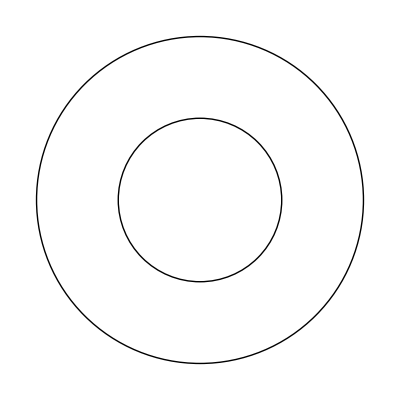

```mathematica
-Graphics--Graphics-
```